## Audio & Video

In Section 12 we saw how the Wolfram Language deals with sounds made up of musical notes. But actually it can handle any kind of audio, including for example human speech. AudioCapture lets you capture audio from a microphone on your computer.

Capture me saying (nonsensically) “a cat, a dog, a squid”:

```mathematica
AudioCapture[]
```

The box represents the audio you’ve captured. You can play it by pressing the . There are many functions for doing operations on it. For example, you can plot audio intensity using AudioPlot.

Make a plot of audio intensity as a function of time:

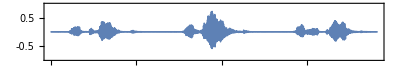

```mathematica
AudioPlot[-Graphics-]
```

In this plot, one can roughly pick out the different words. A more detailed way to visualize audio is to use a spectrogram. A spectrogram is a bit like a generalized musical score, in which a higher intensity at a given pitch is shown darker.

Generate a spectrogram for the audio:

```mathematica
Spectrogram[-Graphics-]
```

-Graphics-

Different vocal sounds, or phonemes, show up as different structures in a spectrogram. SpeechRecognize tries to analyze the whole spectrogram to recognize words. For a long piece of audio, there’s a lot of computation involved, so it can take a while.

Recognize what’s being said in the audio:

```mathematica
SpeechRecognize[-Graphics-]
```

A cat, a dog, a squid.

Pitch-shifting the audio by a factor of 2 (i.e. one octave) makes my voice high pitched and goofy sounding. The spectrogram for it is stretched.

Make a spectrogram for a pitch-shifted version of the audio:

```mathematica
Spectrogram[AudioPitchShift[-Graphics-,2]]
```

-Graphics-

SpeechRecognize no longer recognizes what’s being said:

```mathematica
SpeechRecognize[AudioPitchShift[-Graphics-,2]]
```

I can't. I don't. I scream.

The Wolfram Language can not only recognize speech, but also generate it. Speak makes your computer speak. SpeechSynthesize gives you the explicit audio.

Synthesize audio from speech, and generate a spectrogram of it:

```mathematica
Spectrogram[SpeechSynthesize["a cat, a dog, a squid"]]
```

-Graphics-

The spectrogram with the computer’s voice looks at least somewhat similar to the one with my voice. On most computers, SpeechSynthesize has access to a range of voices with different accents, here described by first names characteristic of where the accents are from.

Use different voices with different accents:

```mathematica
Spectrogram[SpeechSynthesize["a cat, a dog, a squid",#]]&/@{"Tessa","Juan","Luca","Lekha"}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

It’s also possible to make audio from the Sound objects we discussed in Section 12.

A sequence of notes (in successive octaves) played on a synthesized piano:

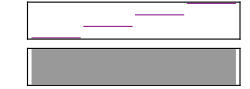

```mathematica
Sound[Table[SoundNote[12n,1,"Piano"],{n,4}]]
```

The corresponding audio plot, with higher-pitched notes decaying faster:

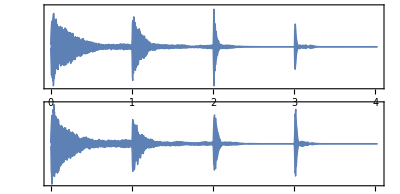

```mathematica
AudioPlot[Sound[Table[SoundNote[12n,1,"Piano"],{n,4}]]]
```

And the spectrogram:

```mathematica
Spectrogram[Sound[Table[SoundNote[12n,1,"Piano"],{n,4}]]]
```

-Graphics-

The corresponding spectrogram for a synthesized violin:

```mathematica
Spectrogram[Sound[Table[SoundNote[12n,1,"Violin"],{n,4}]]]
```

-Graphics-

The analog of ImageIdentify for audio is AudioIdentify.

AudioIdentify identifies the audio as being from a violin:

```mathematica
AudioIdentify[Sound[Table[SoundNote[12n,1,"Violin"],{n,4}]]]
```

violin

The Wolfram Language works not only with audio, but also with video. VideoCapture captures video from your computer’s camera.

Capture a short video of me:

```mathematica
VideoCapture[]
```

Get a list of frames from the video as images:

```mathematica
VideoFrameList[,6]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Extract the audio track from the video and figure out what I said:

```mathematica
SpeechRecognize[Audio[]]
```

Hello there, let me introduce you to my spiky friend.

Compute average red, green and blue in the course of the video:

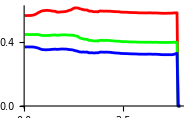

```mathematica
ListLinePlot[VideoMapTimeSeries[Mean[#Image]&,],PlotStyle->{Red,Green,Blue}]
```

Instead of directly capturing a video, you can get it from a file or stream it from a server. You can also create a video using a program.

AnimationVideo works like Manipulate, except that it automatically animates and produces a video of the result. The video will often involve a very large amount of data, so it may take a while to generate.

Generate a video of a black disk “growing” inside a yellow disk:

```mathematica
AnimationVideo[Graphics[{Style[Disk[{0,0},1],Yellow],Style[Disk[{0,0},a],Black]},ImageSize->100],{a,0,1}]
```

Save the video as an .mp4 file:

```mathematica
Export["blob.mp4",%]
```

Like in Manipulate, you can specify a step size in AnimationVideo.

Generate a video of pie charts with between 1 and 10 segments:

```mathematica
AnimationVideo[PieChart[Table[1,n],ImageSize->100],{n,1,10,1}]
```

Vocabulary

AudioCapture[] |   | capture audio from your computer’s microphone
AudioPlot[audio] |   | plot sound intensity in audio
Spectrogram[audio] |   | generate a spectrogram from audio
AudioPitchShift[audio,r] |   | shift the pitch of audio
SpeechRecognize[audio] |   | recognize words in audio
Speak["string"] |   | speak a string
SpeechSynthesize["string"] |   | synthesize audio of speech 
AudioIdentify[audio] |   | identify what audio is of
VideoCapture[] |   | capture video from your computer’s camera
VideoFrameList[video,n] |   | generate a list of frames from a video
VideoMapTimeSeries[f,video] |   | apply a function to each frame of a video
AnimationVideo[expr,{t,min,max}] |   | generate a video by animating an expression

"12 Exercises Available" | "Get Started »"

Make a spectrogram of the synthesized audio for the number 123456, spoken as “1 million, ...”. »

| Expected output: |  
  | -Graphics- |

Make a spectrogram of the synthesized audio for the longest word in English (as given by WordList[]). »

| Expected output: |  
  | -Graphics- |

Synthesize audio of the spoken English alphabet. (Put spaces between letters so they’re said separately.) »

| Expected output: |  
  |  |

Make a spectrogram of the synthesized audio of the spoken English alphabet. »

| Expected output: |  
  | -Graphics- |

Synthesize speech for the word “hello”, pitch shifted up by a factor 2 in frequency. »

| Sample expected output: |  
  |  |

Make a table of the result of trying to recognize synthesized speech of the word “computer”, pitch shifted by factors from 1 to 1.5 in steps of 0.1. »

| Expected output: |  
  | {"Computer.","Computer.","Computer.","Computer.", "Computer.","Computer."} |

Make an audio plot of synthesized notes 0, 12, 24 played for 1 second each on a guitar. »

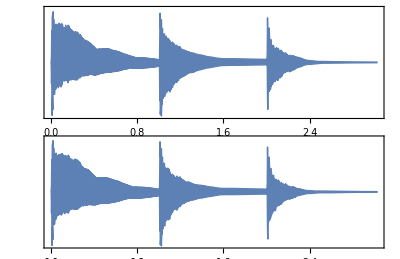
| Expected output: |  
  | -Graphics- |

Make a table of the audio identifications for pitch-shifted versions of note 0 played on a synthesized trumpet for 1 second, with pitch shifts by factors from 0.5 to 1 in steps of 0.1. »

| Expected output: |  
  | {"trombone","trombone","trombone","trombone","trumpet","trumpet"} |

Create a video that shows progressively less blurred versions of an image (from CurrentImage[] or elsewhere). The blurring should start at 20 pixels and go down to 0. »

| Expected output: |  
  |  |

Make a video of regular polygons with between 3 and 20 sides, inscribed in a circle. »

| Expected output: |  
  |  |

Make a video of a disk with a hue going from 0 to 1. Make the video of size 50. »

| Expected output: |  
  |  |

Make a video running through letters of the uppercase alphabet rendered at size 200. »

| Expected output: |  
  |  |

Q&A

How do I specify which microphone I want to use to capture audio?

You can set it in the AudioCapture GUI, or you can explicitly set $DefaultAudioInputDevice.

What voice styles can SpeechSynthesize use?

It depends on your computer system. $VoiceStyles gives a list; VoiceStyleData[] gives more information.

How long an audio file can the Wolfram Language handle?

There’s no built-in limit. But operations like SpeechRecognize can take a while, often roughly the same time as it would take to play the audio.

What does a spectrogram actually show?

The horizontal axis is time; the vertical axis is frequency. The darkness shows the intensity of sound at a particular frequency at a given time. Technically, a spectrogram shows discrete Fourier transforms of the audio signal over short periods of time.

Can one pick out particular letters or sounds in voice spectrograms?

Vowels are typically associated with roughly horizontal bands corresponding to sounds with slowly changing specific frequencies. Consonants tend to be associated with vertical bands involving a range of frequencies. The hiss-like “s” sound in “squid” is an example.

Why are there multiple lines for each note in the music spectrograms?

They correspond to harmonics. The lowest line is at the fundamental frequency of the note. The higher ones are higher harmonics, associated with different modes of oscillation of piano or violin strings. PitchRecognize tries to pick out the fundamental frequency for a note.

How do I specify which camera I want to use to capture video?

You can set it in the VideoCapture GUI, or you can explicitly set $DefaultImagingDevice.

What video formats can the Wolfram Language handle?

Hundreds of formats and subformats, including all the standard ones, like .mp4, .avi and .mkv. $VideoEncoders and $VideoDecoders list them. VideoTranscode converts between them.

What does VideoMapTimeSeries do?

It applies the function you specify to an association (with keys "Time", "Image", etc.) corresponding to each frame of the video, then assembles the results into a TimeSeries object.

Tech Notes

Audio and Video are symbolic objects that represent audio and video. They have many properties that can be queried.

Audio and Video typically involve large amounts of data, which is normally stored in separate external files rather than directly in notebooks. Usually those files will be local to your computer. But $GeneratedAssetLocation lets you specify where you want the data stored. "CloudObject" says to put the data in the Wolfram Cloud, where it’s possible to access it from other computers.

AudioTimeStretch lets you make audio faster or slower, without changing the pitch.

AudioPlot plots the waveform of the sound. If you zoomed in far enough, you’d see the oscillations your speaker has to make to produce the sound.

Spectrogram by default uses a linear scale of frequency, while musical scores effectively use a logarithmic scale (corresponding to pitch).

You can do arithmetic on Audio objects, for example changing volume by multiplying by a constant.

VideoScreenCapture makes a video by capturing what’s going on in a region of your computer screen.

VideoFrameList by default picks out frames that are equally spaced in time.

FrameListVideo makes a video from a list of frames.

Images assembled as frames of a video all need to be the same size. Often you can ensure this with ImageSize. You can also use ConformImages.

More to Explore

Guide to Audio in the Wolfram Language »

Guide to Speech Processing in the Wolfram Language »

Guide to Video in the Wolfram Language »